# Decision boundary Theory

```mathematica
fnew[fbase_, steps_, L_, r_, delta_] = (fbase * L - fbase  - r * Sum[((delta/(1+r))^t)*(fbase * L - fbase * t),{t, 1,steps}])/(L - 1 - r * Sum[((delta/(1+r))^t)*(t - L),{t, 1,steps}])
f[fbase_, steps_, L_, r_, delta_] = (L - 1 - r * Sum[((delta/(1+r))^t)*(fbase * L - fbase * t),{t, 1,steps}])/(L - 1 - r * Sum[((delta/(1+r))^t)*(L - t),{t, 1,steps}])
```

(-fbase+fbase L-(delta fbase r (-1+L-delta L-r+L r+(delta/(1+r))^steps-L (delta/(1+r))^steps+delta L (delta/(1+r))^steps+r (delta/(1+r))^steps-L r (delta/(1+r))^steps+(delta/(1+r))^steps steps-delta (delta/(1+r))^steps steps+r (delta/(1+r))^steps steps))/(-1+delta-r)^2)/(-1+L+(delta r (-1+L-delta L-r+L r+(delta/(1+r))^steps-L (delta/(1+r))^steps+delta L (delta/(1+r))^steps+r (delta/(1+r))^steps-L r (delta/(1+r))^steps+(delta/(1+r))^steps steps-delta (delta/(1+r))^steps steps+r (delta/(1+r))^steps steps))/(-1+delta-r)^2)

(-1+L-(delta fbase r (-1+L-delta L-r+L r+(delta/(1+r))^steps-L (delta/(1+r))^steps+delta L (delta/(1+r))^steps+r (delta/(1+r))^steps-L r (delta/(1+r))^steps+(delta/(1+r))^steps steps-delta (delta/(1+r))^steps steps+r (delta/(1+r))^steps steps))/(-1+delta-r)^2)/(-1+L-(delta r (-1+L-delta L-r+L r+(delta/(1+r))^steps-L (delta/(1+r))^steps+delta L (delta/(1+r))^steps+r (delta/(1+r))^steps-L r (delta/(1+r))^steps+(delta/(1+r))^steps steps-delta (delta/(1+r))^steps steps+r (delta/(1+r))^steps steps))/(-1+delta-r)^2)

```mathematica
(-1+L-(delta fbase r (-1+L-delta L-r+L r+(delta/(1+r))^steps-L (delta/(1+r))^steps+delta L (delta/(1+r))^steps+r (delta/(1+r))^steps-L r (delta/(1+r))^steps+(delta/(1+r))^steps steps-delta (delta/(1+r))^steps steps+r (delta/(1+r))^steps steps))/(-1+delta-r)^2)/(-1+L-(delta r (-1+L-delta L-r+L r+(delta/(1+r))^steps-L (delta/(1+r))^steps+delta L (delta/(1+r))^steps+r (delta/(1+r))^steps-L r (delta/(1+r))^steps+(delta/(1+r))^steps steps-delta (delta/(1+r))^steps steps+r (delta/(1+r))^steps steps))/(-1+delta-r)^2)
```

(-1+L-(delta fbase r (-1+L-delta L-r+L r+(delta/(1+r))^steps-L (delta/(1+r))^steps+delta L (delta/(1+r))^steps+r (delta/(1+r))^steps-L r (delta/(1+r))^steps+(delta/(1+r))^steps steps-delta (delta/(1+r))^steps steps+r (delta/(1+r))^steps steps))/(-1+delta-r)^2)/(-1+L-(delta r (-1+L-delta L-r+L r+(delta/(1+r))^steps-L (delta/(1+r))^steps+delta L (delta/(1+r))^steps+r (delta/(1+r))^steps-L r (delta/(1+r))^steps+(delta/(1+r))^steps steps-delta (delta/(1+r))^steps steps+r (delta/(1+r))^steps steps))/(-1+delta-r)^2)

30

{{1.25,1.20665,1.17088,1.14126,1.11666,1.09618,1.07911,1.06486,1.05298,1.04306,1.03479,1.0279,1.02218,1.01743,1.01351,1.01027,1.00761,1.00543,1.00366,1.00224,1.00109,1.00018,0.999473,0.998924,0.998508,0.998203,0.997988,0.997846,0.997762,0.997725,0.997725},{1.5,1.44798,1.40506,1.36952,1.33999,1.31541,1.29493,1.27783,1.26357,1.25167,1.24175,1.23349,1.22662,1.22092,1.21621,1.21232,1.20913,1.20652,1.2044,1.20268,1.20131,1.20022,1.19937,1.19871,1.19821,1.19784,1.19759,1.19741,1.19731,1.19727,1.19727},{1.75,1.68931,1.63924,1.59777,1.56332,1.53465,1.51075,1.49081,1.47417,1.46028,1.44871,1.43907,1.43105,1.42441,1.41891,1.41438,1.41065,1.40761,1.40513,1.40313,1.40153,1.40026,1.39926,1.39849,1.39791,1.39748,1.39718,1.39698,1.39687,1.39681,1.39681},{2.,1.93064,1.87341,1.82602,1.78666,1.75389,1.72657,1.70378,1.68476,1.66889,1.65566,1.64465,1.63549,1.62789,1.62161,1.61643,1.61217,1.60869,1.60586,1.60358,1.60175,1.60029,1.59916,1.59828,1.59761,1.59713,1.59678,1.59655,1.59642,1.59636,1.59636}}

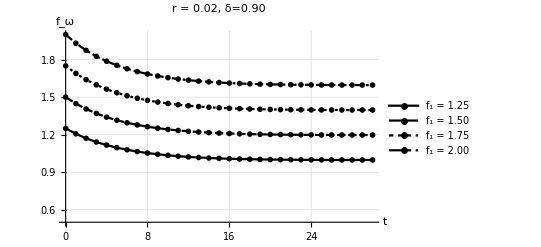

```mathematica
layers = 30
data = Table[Table[fnew[factor,x,layers,0.02,0.9], {x,0,layers,1}], {factor, 1.25, 2., 0.25}]
ListLinePlot[data, PlotTheme->"Monochrome", PlotRange -> {0.5, 2.0}, AxesLabel->{"t", "f_ω"},PlotLabel-> "r = 0.02, δ=0.90", PlotLegends->{"f_1 = 1.25", "f_1 = 1.50", "f_1 = 1.75", "f_1 = 2.00"}, GridLines->Automatic, DataRange->{0, layers}]
```

```mathematica
XCLAIM
```

```mathematica
buffer = (1 + 0.1706) * (1 + 0.7634) 
f1 = 1 * buffer
```

2.06424

2.06424

12

{2.06424,1.99264,1.93699,1.89387,1.86069,1.83545,1.81658,1.80282,1.79317,1.78681,1.78307,1.78143,1.78143}

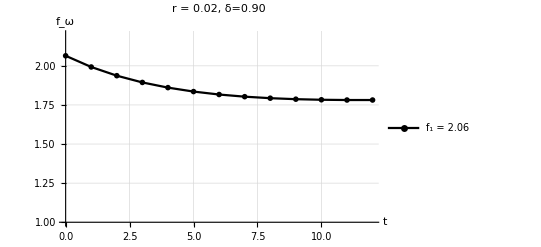

```mathematica
layers = 12
data = Table[fnew[f1,x,layers,0.02,0.9], {x,0,layers,1}]
ListLinePlot[data, PlotTheme->"Monochrome", PlotRange -> {1.0, 2.2}, AxesLabel->{"t", "f_ω"},PlotLabel-> "r = 0.02, δ=0.90", PlotLegends->{"f_1 = 2.06"}, GridLines->Automatic, DataRange->{0, layers}]
```

```mathematica
fomega = Last[data]
```

1.77861

```mathematica
1.8518166645938126
reduction = 1 - (fomega/f1)
```

1.85182

0.13837